```mathematica
Modulo[r_List,rb_List]:=Sqrt[(r[[1]]-rb[[1]])^2+(r[[2]]-rb[[2]])^2];(*Funcion para obtener la distancia entre dos vectores*)
Ce[r_,ro_,q_:1]:= (r-ro) Divide[q,4 π Modulo[r,ro]^3];(*Funcion para el campo electrico a partir del vector r, el posicion de particula y el vector orige ro*)
A={{va,vb},{1,3}};(*A contiene toda la info, la pos. de particulas en la primera lista y sus cargas q en la segunda lista*)
SumC[A_]:=Sum[Ce[A[[1]][[i]]],{x,y},A[[2]][[i]],{i,Length[A[[2]]]}];(*Funcion para sumar los campos Electricos, donde A es la data de las particulas y N=Lenght[A[[2]]] es el numero de particulas*)
```

```mathematica
Ce[vb,va,4]
```

{1/(5 √5 π),-2/(5 √5 π)}

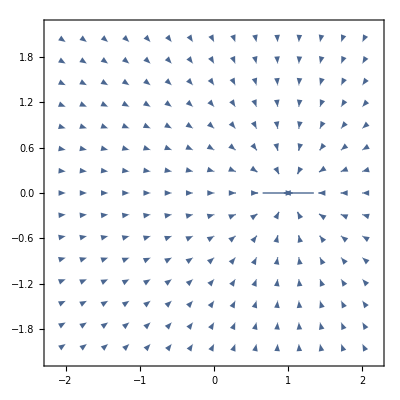

```mathematica
VectorPlot[{Ce[vb,{x,y},6]},{x,-2,2},{y,-2,2}]
```

```mathematica
Modulo[{1,2},{0,2}]
```

1